#### Zr96

```mathematica
ClearAll["Global`*"]
```

```mathematica
strBMZr={0.0000024402,0.0000073572,0.0000209852,0.0000566281,0.0001445673,0.0003491628,0.0007978232,0.0017246781,0.0035272428,0.0068248597,0.0124937137,0.0216392578,0.0354623999,0.0549926175,0.0807065336,0.1121176563,0.1474858364,0.1838140833,0.2172427572,0.2438161074,0.2604292492,0.2656442305,0.2600651055,0.2461053108,0.2272137929,0.2068438097,0.1875461817,0.1705009746,0.1556043023,0.1419968647,0.1287627359,0.1155015629,0.1025776111,0.0910128797,0.0821389498,0.0771948624,0.0770406597,0.0820735526,0.0923328188,0.1077055637,0.1281250527,0.1536887538,0.1846951052,0.2216728560,0.2655163289,0.3178117969,0.3813308583,0.4604963555,0.5614595029,0.6913662835,0.8565418220,1.0597244895,1.2970465412,1.5559452309,1.8152855279,2.0484656163,2.2292133571,2.3385525878,2.3706044447,2.3349704305,2.2545072540,2.1589510480,2.0763844203,2.0253233061,2.0099504207,2.0199015135,2.0344879916,2.0298534620,1.9867316598,1.8964079689,1.7631640540,1.6026678012,1.4370663211,1.2885213311,1.1732869177,1.0980951107,1.0597502955,1.0477537995,1.0488268371,1.0516515919,1.0501695918,1.0443730861,1.0385228431,1.0377758269,1.0448872691,1.0586458179,1.0749607315,1.0903238901,1.1062104222,1.1323510830,1.1869850503,1.2931508809,1.4714932715,1.7315004554,2.0640598724,2.4383223752,2.8048865453,3.1053848396,3.2862373162,3.3125339895,3.1775813302,2.9049611397,2.5425595266,2.1508315011,1.7893642406,1.5058958881,1.3304733544,1.2751976862,1.3380050125,1.5078799957,1.7690102648,2.1024270506,2.4851406886,2.8881025537,3.2750219320,3.6038616885,3.8317710226,3.9226762098,3.8553718877,3.6293612415,3.2662091371,2.8056385558,2.2974163931,1.7914717347,1.3291046141,0.9374818483,0.6282660781,0.3998178925,0.2414967704,0.1383918126,0.0752145638,0.0387568434,0.0189290833,0.0087607345,0.0038414002,0.0015954996,0.0006276135,0.0002337844,0.0000824543,0.0000275321,0.0000087027,0.0000026039,0.0000007374,0.0000001977,0.0000000501,0.0000000120,0.0000000027,0.0000000006,0.0000000001,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000};
enBMZr={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
strBPZr={0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000001,0.0000000002,0.0000000004,0.0000000010,0.0000000023,0.0000000048,0.0000000096,0.0000000180,0.0000000319,0.0000000535,0.0000000851,0.0000001280,0.0000001824,0.0000002462,0.0000003156,0.0000003853,0.0000004511,0.0000005125,0.0000005768,0.0000006622,0.0000008004,0.0000010361,0.0000014234,0.0000020171,0.0000028613,0.0000039736,0.0000053316,0.0000068641,0.0000084518,0.0000099417,0.0000111712,0.0000119998,0.0000123380,0.0000121659,0.0000115354,0.0000105565,0.0000093713,0.0000081254,0.0000069424,0.0000059092,0.0000050711,0.0000044354,0.0000039797,0.0000036617,0.0000034289,0.0000032280,0.0000030138,0.0000027566,0.0000024455,0.0000020887,0.0000017084,0.0000013331,0.0000009898,0.0000006981,0.0000004671,0.0000002963,0.0000001780,0.0000001013,0.0000000546,0.0000000278,0.0000000134,0.0000000061,0.0000000026,0.0000000011,0.0000000004,0.0000000002,0.0000000001,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000001,0.0000000001,0.0000000004,0.0000000009,0.0000000021,0.0000000046,0.0000000095,0.0000000187,0.0000000350,0.0000000622,0.0000001054,0.0000001706,0.0000002642,0.0000003927,0.0000005618,0.0000007762,0.0000010397,0.0000013546,0.0000017222,0.0000021422,0.0000026122,0.0000031261,0.0000036730,0.0000042355,0.0000047892,0.0000053027,0.0000057391,0.0000060594,0.0000062271,0.0000062151,0.0000060111,0.0000056226,0.0000050777,0.0000044218,0.0000037108,0.0000030017,0.0000023437,0.0000017715,0.0000013024,0.0000009374,0.0000006658,0.0000004702,0.0000003318,0.0000002342,0.0000001646,0.0000001143,0.0000000777,0.0000000512,0.0000000325,0.0000000197,0.0000000114,0.0000000063,0.0000000033,0.0000000016,0.0000000008,0.0000000003,0.0000000001,0.0000000001,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000};
enBPZr={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
```

#### Mo96

```mathematica
strBPMo={0.0000496431,0.0000894522,0.0001531489,0.0002490863,0.0003847935,0.0005645347,0.0007865230,0.0010406682,0.0013079641,0.0015623968,0.0017755158,0.0019227343,0.0019894750,0.0019749709,0.0018921596,0.0017635219,0.0016143125,0.0014656609,0.0013299927,0.0012101363,0.0011018885,0.0009984637,0.0008947317,0.0007895991,0.0006859707,0.0005888631,0.0005029147,0.0004305323,0.0003713728,0.0003231223,0.0002829845,0.0002491047,0.0002213453,0.0002012118,0.0001911018,0.0001932657,0.0002088870,0.0002375599,0.0002772478,0.0003246402,0.0003757244,0.0004263784,0.0004728380,0.0005119793,0.0005414286,0.0005595669,0.0005655004,0.0005590602,0.0005408604,0.0005124174,0.0004763036,0.0004362957,0.0003974640,0.0003661575,0.0003498334,0.0003566810,0.0003949783,0.0004721309,0.0005933972,0.0007604244,0.0009698800,0.0012126159,0.0014738658,0.0017348734,0.0019760753,0.0021815439,0.0023439485,0.0024689228,0.0025775536,0.0027057772,0.0028998259,0.0032075328,0.0036663070,0.0042898807,0.0050572406,0.0059079027,0.0067471066,0.0074621012,0.0079468047,0.0081281513,0.0079854093,0.0075552005,0.0069198278,0.0061829007,0.0054411953,0.0047628161,0.0041785507,0.0036874746,0.0032721689,0.0029158316,0.0026140487,0.0023772838,0.0022244451,0.0021713483,0.0022194078,0.0023492892,0.0025221142,0.0026880031,0.0027992019,0.0028235368,0.0027539329,0.0026112133,0.0024398131,0.0022984592,0.0022493394,0.0023492791,0.0026450331,0.0031726056,0.0039584316,0.0050191255,0.0063569224,0.0079499802,0.0097398186,0.0116211607,0.0134407809,0.0150105161,0.0161352429,0.0166507277,0.0164612240,0.0155649863,0.0140587260,0.0121186597,0.0099635941,0.0078112090,0.0058400486,0.0041664817,0.0028398270,0.0018527537,0.0011602826,0.0007001118,0.0004089349,0.0002324249,0.0001291908,0.0000704957,0.0000378265,0.0000199385,0.0000102883,0.0000051706,0.0000025167,0.0000011800,0.0000005304,0.0000002278,0.0000000932,0.0000000362,0.0000000134,0.0000000047,0.0000000016,0.0000000005,0.0000000001,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000};
enBPMo={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
```

## Figure 1

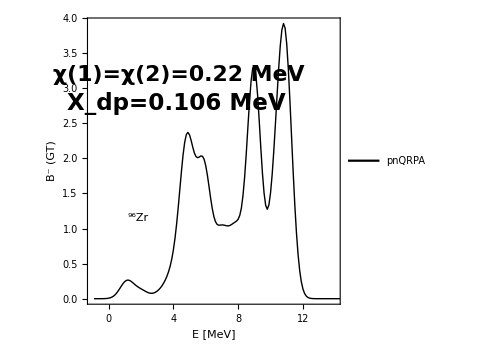

```mathematica
tableFig1=Table[{enBMZr[[i]],strBMZr[[i]]},{i,1,Length[strBMZr]}];
fig1=ListPlot[tableFig1,Joined->True,ImageSize->Medium,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{-1,14},Full},FrameLabel->{"E [MeV]","B^- (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.35,0.9}],Epilog->{Inset[Style["χ(1)=χ(2)=0.22 MeV",22,Bold,Black,FontFamily->"Times"],Scaled[{0.36,0.8}]],Inset[Style["X_dp=0.106 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.7}]],Inset[Framed[Style[Row[{Superscript["","96"],"Zr"}],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.2,0.3}]]},ImageSize->350];
Show[fig1]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_1/new_figs/fig2_set1.pdf",Show[fig1],ImageResolution->1200];
```

## Figure 2

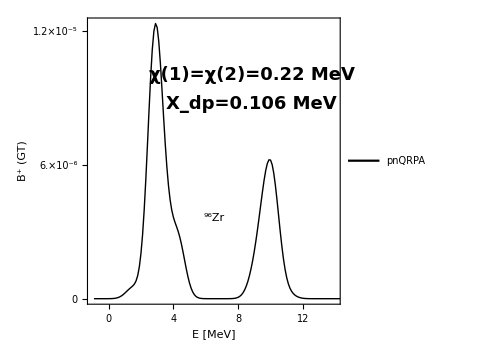

```mathematica
tableFig2=Table[{enBPZr[[i]],strBPZr[[i]]},{i,1,Length[strBPZr]}];
(*ListPlot[tableFig2,Ticks->{Automatic,{#,ScientificForm@#}&/@{0,0.000006,0.000012}},PlotRange->All]*)
fig2=ListPlot[tableFig2,Joined->True,ImageSize->Medium,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{18,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.65,0.9}],PlotRange->{{-1,14},Full},(*FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}}*)FrameTicks->{{{#,ScientificForm@#}&/@{0,0.000006,0.000012},Automatic},{Automatic,Automatic}},Epilog->{Inset[Style["χ(1)=χ(2)=0.22 MeV",18,Bold,Black,FontFamily->"Times"],Scaled[{0.65,0.8}]],Inset[Style["X_dp=0.106 MeV",18,Bold,Black,FontFamily->"Times"],Scaled[{0.65,0.7}]],Inset[Framed[Style[Row[{Superscript["","96"],"Zr"}],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.5,0.3}]]},ImageSize->350];
Show[fig2]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_1/new_figs/fig2_set1.pdf",Show[fig2],ImageResolution->1200];
```

## Figure 3

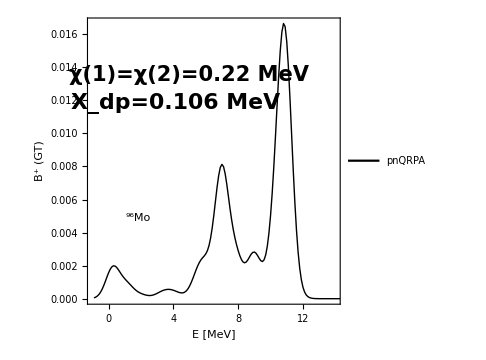

```mathematica
tableFig3=Table[{enBPMo[[i]],strBPMo[[i]]},{i,1,Length[strBPMo]}];
fig3=ListPlot[tableFig3,Joined->True,ImageSize->Medium,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.35,0.9}],PlotRange->{{-1,14},Full},Epilog->{Inset[Style["χ(1)=χ(2)=0.22 MeV",21,Bold,Black,FontFamily->"Times"],Scaled[{0.4,0.8}]],Inset[Style["X_dp=0.106 MeV",22,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.7}]],Inset[Framed[Style[Row[{Superscript["","96"],"Mo"}],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.2,0.3}]]},ImageSize->350];
Show[fig3]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_1/new_figs/fig3_set1.pdf",Show[fig3],ImageResolution->1200];
```